## Definicje

### Stałe

```mathematica
np=1.4537;(* fused silica *)
(*np=1.5112;(* bk7 *)*)
nm=0.18212+ⅈ 4.5473;
nspow={ns-> 1.0002752};
nshelu={ns-> 1.000035};
dpod=37.5 10^-9;
dopt=45 10^-9;
λnow=780 10^-9;
```

### Wspólne definicje

```mathematica
AppendTo[$Path, NotebookDirectory[]];
controlSize=Small;
controlParams=Sequence[Appearance->{"Open", Tiny},ImageSize->180,AppearanceElements->{"StepLeftButton","InputField","StepRightButton"}];
WP[theta_,phi_]:= {{Cos[theta]*Cos[theta]*Exp[I*phi/2] + Sin[theta]*Sin[theta]*Exp[-1*I*phi/2], Cos[theta]*Sin[theta]*2*I*Sin[phi/2]}, {Cos[theta]*Sin[theta]*2*I*Sin[phi/2], Cos[theta]*Cos[theta]*Exp[-1*I*phi/2] + Sin[theta]*Sin[theta]*Exp[I*phi/2]}} ;
POL[analiz_]:={{Cos[analiz]^2,Cos[analiz]Sin[analiz]},{Cos[analiz]Sin[analiz],Sin[analiz]^2}};
EOM[U_]:=WP[0.25π,(π/2)*(U/200)];
plotSize={240,240};
ParamPlot[input_,zoom_:1.0]:=ParametricPlot[(((Abs@input)){Cos[ϕ],Cos[ϕ+Differences@Arg@input]}),{ϕ,0,2π},PlotRange->{{-1,1}/zoom,{-1,1}/zoom},AspectRatio->1,AxesLabel->{"p","s"},ImageSize->plotSize];
GEN[t_]:=TriangleWave[t];
```

```mathematica
Needs["NumericalCalculus`"]
β[θ_,d_,λ_]:=2π Sqrt[nm^2-np^2 Sin[θ]^2]d/λ;
qs[nj_,θ_]:=nj Sqrt[1-(np/nj)^2 Sin[θ]^2];
qp[nj_,θ_]:=(1/nj) Sqrt[1-(np/nj)^2 Sin[θ]^2];
r[i_,t_]:=(i-t)/(i+t);
rspm[θ_]:=r[qs[np,θ],qs[nm,θ]];
rsms[θ_]:=r[qs[nm,θ],qs[ns,θ]];

rppm[θ_]:=r[qp[np,θ],qp[nm,θ]];
rpms[θ_]:=r[qp[nm,θ],qp[ns,θ]];
rstot[θ_,d_,λ_]:=(rspm[θ]+rsms[θ]Exp[2ⅈ β[θ,d,λ]])/(1+rspm[θ]rsms[θ]Exp[2ⅈ β[θ,d,λ]]);
rptot[θ_,d_,λ_]:=(rppm[θ]+rpms[θ]Exp[2ⅈ β[θ,d,λ]])/(1+rppm[θ]rpms[θ]Exp[2ⅈ β[θ,d,λ]]);
θo[θi_]:= ArcSin[Sin[θi/np]]+π/4;

fazaaut=Exp[ⅈ π /2];
faza=Exp[ⅈ π 7/10];
roznicaObecnie[θ_]:=+Arg[faza rstot[θo[θ],dpod,λnow]]-Arg[faza rptot[θo[θ],dpod,λnow]];
roznicaOptymalnie[θ_]:=+Arg[faza rstot[θo[θ],dopt,λnow]]-Arg[faza rptot[θo[θ],dopt,λnow]];
```

```mathematica
LeftDensityPlot[zlist_,colors_:"TemperatureMap"]:=ListDensityPlot[zlist,DataRange->{{nsmin,nsmax},{phimin/Degree,phimax/Degree}},FrameLabel->{"n_s","ϕ [°]"},ColorFunction->colors, PlotRange->Full,FrameTicks->{{All,None},{All,None}},ImageSize->200, MeshFunctions->{#3&},Mesh->5,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}}],Right]];

RightDensityPlot[zlist_,colors_:"TemperatureMap"]:=ListDensityPlot[zlist,DataRange->{{nsmin,nsmax},{phimin/Degree,phimax/Degree}},FrameTicks->{{None,All},{All,None}}, FrameLabel->{"n_s",None,None,"ϕ [°]"},ColorFunction->colors, PlotRange->Full, MeshFunctions->{#3&},ImageSize->200,Mesh->5,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{-10,-10},{5,5}}],Left]];
```

```mathematica
AzotPlot[n1_,n2_]:=Module[{a,b,min,diff},
a=Import["Azot/TEK000"<>n1<>".CSV","Data"];
b=Import["Azot/TEK000"<>n2<>".CSV","Data"];
min=Min[Length@a,Length@b];
diff=Last@Last@MovingAverage[a,Length@a]-Last@Last@MovingAverage[b,Length@b];
ListLinePlot[{
{100#[[1]],#[[2]]}&/@((a[[1;;min,{1,2}]]ᵀ-{a[[1,1]],0})ᵀ),
{100#[[1]],#[[2]]}&/@((b[[1;;min,{1,2}]]ᵀ-{a[[1,1]],0})ᵀ)}, PlotRange->All, Frame->True,FrameLabel->{"t [ms]","U [V]"},Axes->False,
PlotLegends->{"Powietrze","Azot"}, AspectRatio->1.5,PlotLabel->"|ΔU|=" <>ToString[ ScientificForm[Abs@diff±(Last@StandardDeviation[a]+Last@StandardDeviation[a])],FormatType->TraditionalForm]]
]
HelPlot[n_,trimleft_:1,trimright_:All]:=Module[{a},
a=Import["Hel/"<>n,"Data"][[trimleft;;trimright,{1,2}]];
ListLinePlot[{0.1#[[1]],Abs@#[[2]]}&/@((aᵀ-{a[[1,1]],a[[1,2]]})ᵀ), PlotRange->All,Frame->True,FrameLabel->{"t [s]","U [V]"},Axes->False,GridLines->Automatic, AspectRatio->0.5
]];
```

## Obliczenia wstępne

### Amplituda wiązki odbitej w funkcji kąta padania na pryzmat θ_i

#### Układ podstawowy

```mathematica
minpod=Minimize[Abs[rptot[θo[θ Degree ],dpod,λnow]]^2/.nspow,θ]
```

{0.0894937,{θ→0.195801}}

```mathematica
halfpod=FindRoot[(Abs[rptot[θo[θ Degree],dpod,λnow]]^2/.nspow)==0.5,{θ,0,0,5},Method->"Secant"]
```

{θ→1.13072}

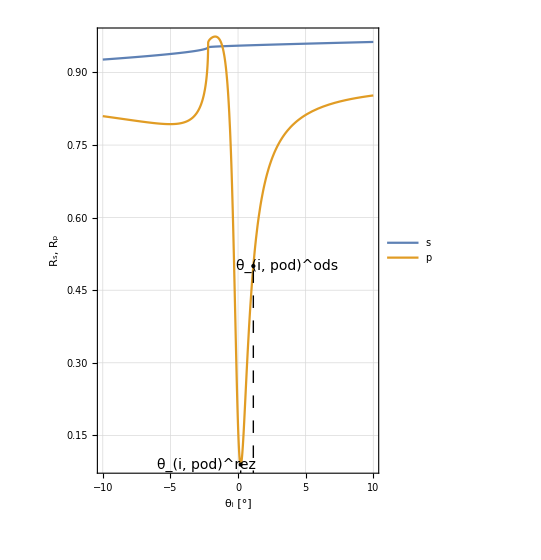

```mathematica
Plot[{Abs[rstot[θo[θ Degree],dpod,λnow]]^2/.nspow,Abs[rptot[θo[θ Degree],dpod,λnow]]^2/.nspow},{θ,-10,10},PlotRange->Full,Frame->True,FrameLabel->{"θ_i [°]","R_s, R_p"},FrameTicks->{{All,None},{All,None}},Axes->False,AspectRatio->1.4, PlotLegends->{"s","p"},Epilog->{PointSize[Medium],Dashing[Medium],Point[{θ/.minpod[[2]],minpod[[1]]}],Line[{{θ/.minpod[[2]],0},{θ/.minpod[[2]],minpod[[1]]}}],Point[{θ/.halfpod,0.5}],Line[{{θ/.halfpod,0},{θ/.halfpod,0.5}}],Text[Style["θ_(i, pod)^rez",14],{-2.5+θ/.minpod[[2]],minpod[[1]]}],Text[Style["θ_(i, pod)^ods",14],{2.5+θ/.halfpod,0.5}]},GridLines->Automatic]
```

#### Układ optymalny

```mathematica
minopt=Minimize[Abs[rptot[θo[θ Degree],dopt,λnow]]^2/.nspow,θ]
```

{0.00279038,{θ→0.0116537}}

```mathematica
halfopt=FindRoot[(Abs[rptot[θo[θ Degree],dopt,λnow]]^2/.nspow)==0.5,{θ,0,0,5},Method->"Secant"]
```

{θ→0.645124}

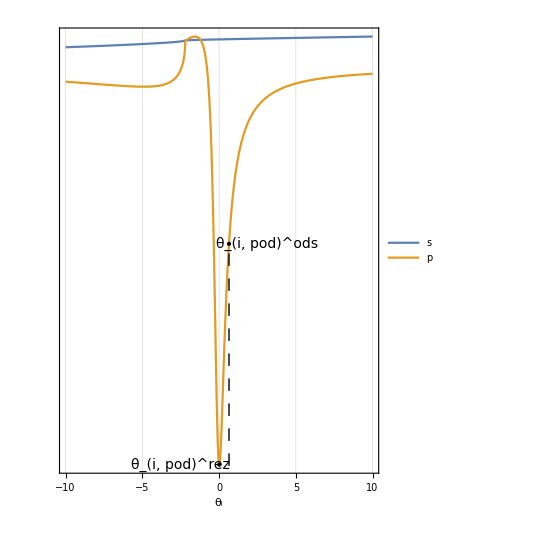

```mathematica
Plot[{Abs[rstot[θo[θ Degree],dopt,λnow]]^2/.nspow,Abs[rptot[θo[θ Degree],dopt,λnow]]^2/.nspow},{θ,-10,10},PlotRange->Full,Frame->True,FrameLabel->{"θ_i",None,None,"R_s, R_p"},FrameTicks->{{None,All},{All,None}},Axes->False,AspectRatio->1.4, PlotLegends->{"s","p"},Epilog->{PointSize[Medium],Dashing[Medium],Point[{θ/.minopt[[2]],minopt[[1]]}],Line[{{θ/.minopt[[2]],0},{θ/.minopt[[2]],minopt[[1]]}}],Point[{θ/.halfopt,0.5}],Line[{{θ/.halfopt,0},{θ/.halfopt,0.5}}],Text[Style["θ_(i, pod)^rez",14],{-2.5+θ/.minopt[[2]],minopt[[1]]}],Text[Style["θ_(i, pod)^ods",14],{2.5+θ/.halfopt,0.5}]},GridLines->Automatic]
```

### Amplituda wiązki odbitej w funkcji współczynnika załamania n_s

#### Układ podstawowy

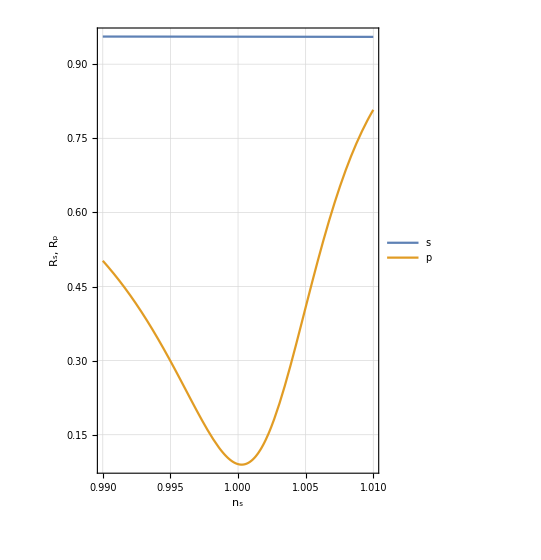

```mathematica
Plot[{Abs[rstot[θo[θ Degree],dpod,λnow]]^2//.minpod⟦2⟧,Abs[rptot[θo[θ Degree],dpod,λnow]]^2//.minpod⟦2⟧},{ns,0.99,1.01},PlotRange->Full, Frame->True,FrameLabel->{"n_s","R_s, R_p"},FrameTicks->{{All,None},{All,None}},Axes->False,AspectRatio->1.4, PlotLegends->{"s","p"},GridLines->Automatic]
```

#### Układ optymalny

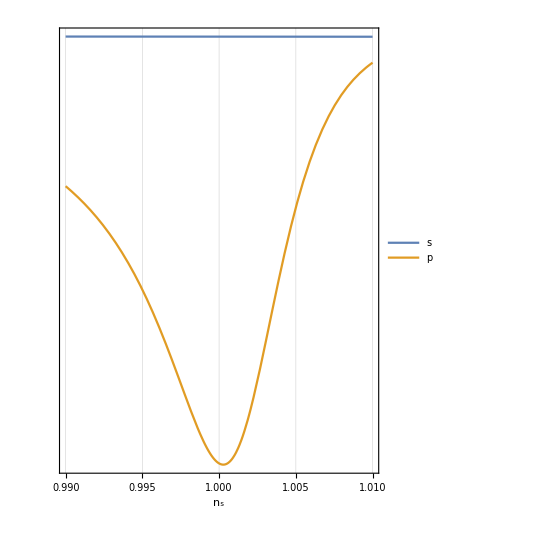

```mathematica
Plot[{Abs[rstot[θo[θ Degree],dopt,λnow]]^2//.minopt⟦2⟧,Abs[rptot[θo[θ Degree],dopt,λnow]]^2//.minopt⟦2⟧},{ns,0.99,1.01},PlotRange->Full, Frame->True,FrameLabel->{"n_s",None,None,"R_s, R_p"},FrameTicks->{{None,All},{All,None}},Axes->False,AspectRatio->1.4, PlotLegends->{"s","p"},GridLines->Automatic]
```

### Faza wiązki odbitej w funkcji kąta padania na pryzmat θ_i

#### Układ podstawowy

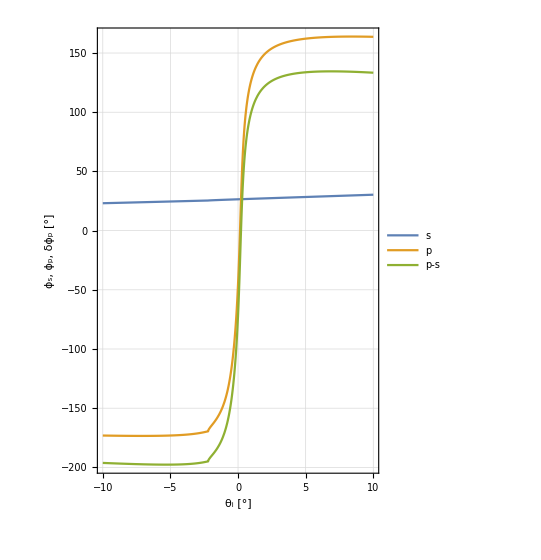

```mathematica
Plot[{-Arg[faza rstot[θo[θ Degree],dpod,λnow]]/Degree/.nspow,-Arg[faza rptot[θo[θ Degree],dpod,λnow]]/Degree/.nspow,roznicaObecnie[θ Degree]/Degree/.nspow},{θ,-10,10},PlotRange->Full,Frame->True,FrameLabel->{"θ_i [°]","ϕ_s, ϕ_p, δϕ_p [°]"},PlotLegends->{"s","p","p-s"},FrameTicks->{{All,None},{All,None}},Axes->False,AspectRatio->1.4,GridLines->Automatic]
```

#### Układ optymalny

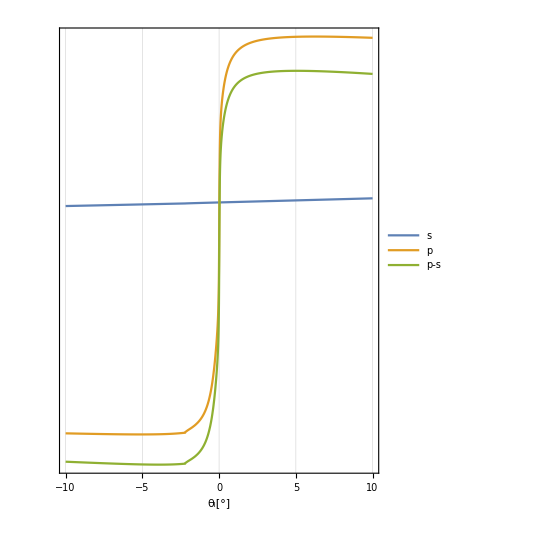

```mathematica
Plot[{-Arg[faza rstot[θo[θ Degree],dopt,λnow]]/Degree/.nspow,-Arg[faza rptot[θo[θ Degree],dopt,λnow]]/Degree/.nspow,roznicaOptymalnie[θ Degree]/Degree/.nspow},{θ,-10,10},PlotRange->Full,Frame->True,FrameLabel->{"θ_i[°]",None,None,"ϕ_s, ϕ_p, δϕ_p [°]"},PlotLegends->{"s","p","p-s"},FrameTicks->{{None,All},{All,None}},Axes->False,AspectRatio->1.4, GridLines->Automatic]
```

### Faza wiązki odbitej w funkcji współczynnika załamania n_s

#### Układ podstawowy

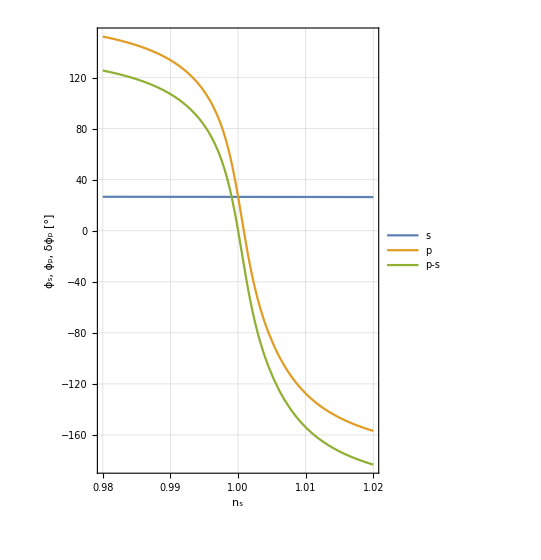

```mathematica
Plot[{-Arg[faza rstot[θo[θ Degree],dpod,λnow]]/Degree/.minpod⟦2⟧,-Arg[faza rptot[θo[θ Degree],dpod,λnow]]/Degree/.minpod⟦2⟧,roznicaObecnie[θ Degree]/Degree/.minpod⟦2⟧},{ns,0.98,1.02},PlotRange->Full,Frame->True,FrameLabel->{"n_s","ϕ_s, ϕ_p, δϕ_p [°]"},PlotLegends->{"s","p","p-s"},FrameTicks->{{All,None},{All,None}},Axes->False,AspectRatio->1.4,GridLines->Automatic]
```

#### Układ optymalny

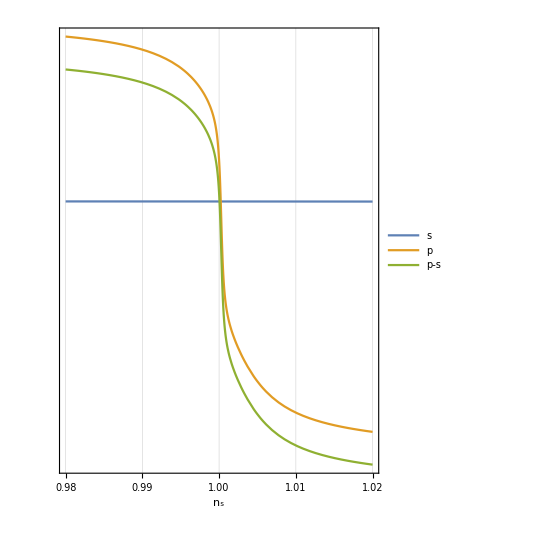

```mathematica
Plot[{-Arg[faza rstot[θo[θ Degree],dopt,λnow]]/Degree/.minopt⟦2⟧,-Arg[faza rptot[θo[θ Degree],dopt,λnow]]/Degree/.minopt⟦2⟧,roznicaOptymalnie[θ Degree]/Degree/.minopt⟦2⟧},{ns,0.98,1.02},PlotRange->Full,Frame->True,FrameLabel->{"n_s",None,None,"ϕ_s, ϕ_p, δϕ_p [°]"},PlotLegends->{"s","p","p-s"},FrameTicks->{{None,All},{All,None}},Axes->False,AspectRatio->1.4,GridLines->Automatic]
```

### Czułość amplitudowa w funkcji współczynnika załamania n_s

#### Układ podstawowy

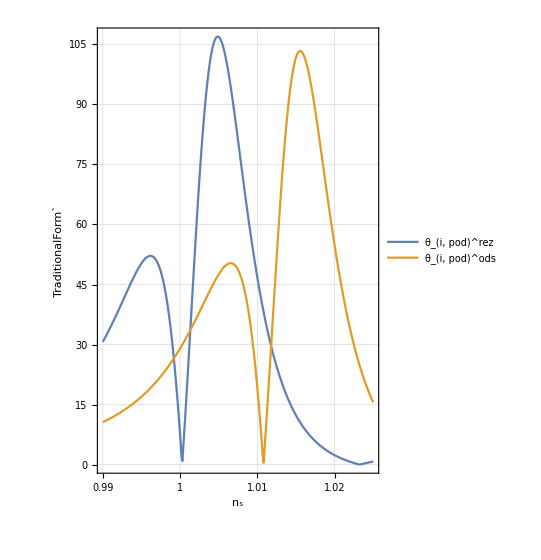

```mathematica
xlist=Table[i,{i,0.99,1.025,0.0001}];
ylist = ND[Abs[rptot[θo[θ Degree],dpod,λnow]]^2/.minpod[[2]],ns,#, Terms->20, WorkingPrecision->10] &/@xlist;
data={xlist,ylist}ᵀ;
ylist2 = ND[Abs[rptot[θo[θ Degree],dpod,λnow]]^2/.halfpod,ns,#, Terms->20, WorkingPrecision->10] &/@xlist;
data2={xlist,ylist2}ᵀ;
ListLinePlot[Abs@{data,data2},PlotRange->Full,Frame->True,FrameLabel->{"n_s","TraditionalForm`"},PlotLegends->{"θ_(i, pod)^rez","θ_(i, pod)^ods"},FrameTicks->{{All,None},{{0.99,1,1.01,1.02},None}},Axes->False,AspectRatio->1.4,GridLines->Automatic]
```

#### Układ optymalny

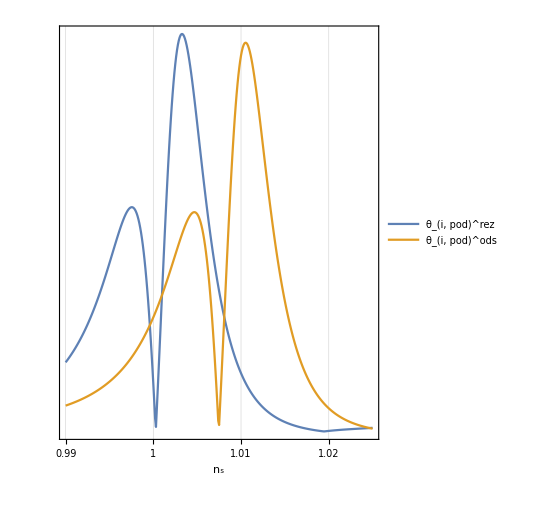

```mathematica
xlist=Table[i,{i,0.990,1.025,0.0001}];
ylist = ND[Abs[rptot[θo[θ Degree],dopt,λnow]]^2/.minopt[[2]],ns,#, Terms->20, WorkingPrecision->10] &/@xlist;
data={xlist,ylist}ᵀ;
ylist2 = ND[Abs[rptot[θo[θ Degree],dopt,λnow]]^2/.halfopt,ns,#, Terms->20, WorkingPrecision->10] &/@xlist;
data2={xlist,ylist2}ᵀ;
ListLinePlot[Abs@{data,data2},PlotRange->Full,Frame->True,FrameLabel->{"n_s",None,None,"TraditionalForm`"},PlotLegends->{"θ_(i, pod)^rez","θ_(i, pod)^ods"},FrameTicks->{{None,All},{{0.99,1,1.01,1.02},None}},Axes->False,AspectRatio->1.3,GridLines->Automatic]
```

### Czułość amplitudowa w funkcji współczynnika załamania n_s

#### Układ podstawowy

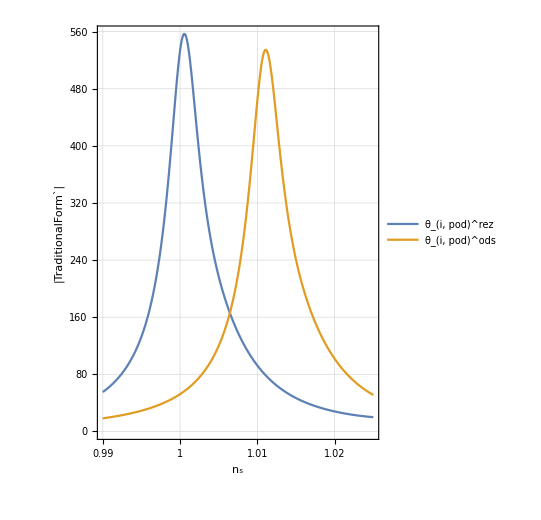

```mathematica
xlist=Table[i,{i,0.99,1.025,.0001}];
ylist = ND[roznicaObecnie[θ Degree]/.minpod[[2]],ns,#, Terms->20, WorkingPrecision->10] &/@xlist;
data={xlist,ylist}ᵀ;
ylist2 = ND[roznicaObecnie[θ Degree]/.halfpod,ns,#, Terms->20, WorkingPrecision->10] &/@xlist;
data2={xlist,ylist2}ᵀ;
ListLinePlot[Abs@{data,data2},PlotRange->Full,Frame->True,FrameLabel->{"n_s","|TraditionalForm`|"},PlotLegends->{"θ_(i, pod)^rez","θ_(i, pod)^ods"},FrameTicks->{{All,None},{{0.99,1,1.01,1.02},None}},Axes->False,AspectRatio->1.3,GridLines->Automatic]
```

#### Układ optymalny

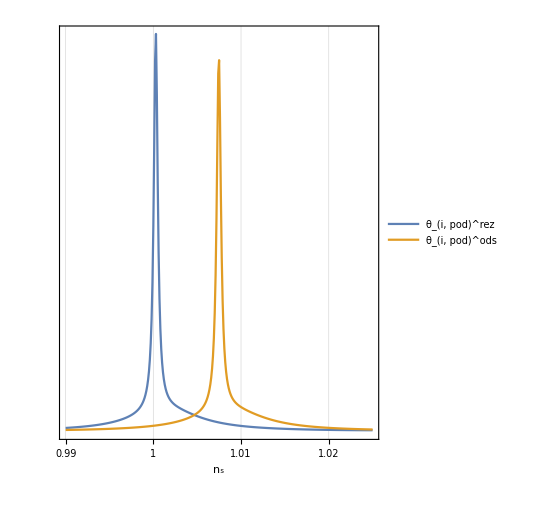

```mathematica
xlist=Table[i,{i,0.99,1.025,.0001}];
ylist = ND[roznicaOptymalnie[θ Degree]/.minopt[[2]],ns,#, Terms->20, WorkingPrecision->10] &/@xlist;
data={xlist,ylist}ᵀ;
ylist2 = ND[roznicaOptymalnie[θ Degree]/.halfopt,ns,#, Terms->20, WorkingPrecision->10] &/@xlist;
data2={xlist,ylist2}ᵀ;
ListLinePlot[Abs@{data,data2},PlotRange->Full,Frame->True,FrameLabel->{"n_s",None,None,"|TraditionalForm`|"},PlotLegends->{"θ_(i, pod)^rez","θ_(i, pod)^ods"},FrameTicks->{{None,All},{{0.99,1,1.01,1.02},None}},Axes->False,AspectRatio->1.3,GridLines->Automatic]
```

## Obliczenia dla konkretnych konfiguracji pomiarowych

```mathematica
nsmin=0.990;
nsmax=1.015;
phimin=0;
phimax=π/4;
xlist=Table[i,{i,nsmin,nsmax,0.0001}];
ylist=Table[i,{i,phimin,phimax,0.01}];
E0={1,0};
SPR={{rptot[θo[θ Degree],d,λnow],0},{0,rstot[θo[θ Degree],d,λnow]}};
```

### Czułość detekcji amplitudowej

#### Intensywność polaryzacji p

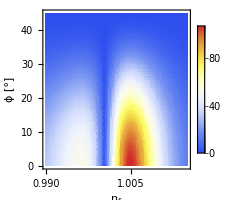

```mathematica
Int=((Abs@(((SPR/.{d->dpod})/.minpod[[2]]).WP[#,π].E0))^2)[[1]] &/@ylist;
LeftDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

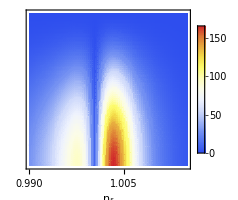

```mathematica
Int=((Abs@(((SPR/.{d->dopt})/.minopt[[2]]).WP[#,π].E0))^2)[[1]] &/@ylist;
RightDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

#### Znormalizowana intensywność polaryzacji p

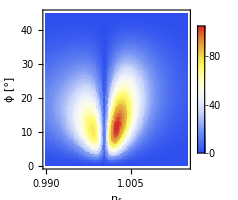

```mathematica
Int=(((Abs@(((SPR/.{d->dpod})/.minpod[[2]]).WP[#,π].E0))^2)[[1]]/Total@((Abs@(((SPR/.{d->dpod})/.minpod[[2]]).WP[# ,π].E0))^2)) &/@ylist;
LeftDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

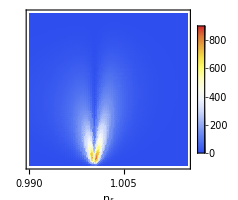

```mathematica
Int=(((Abs@(((SPR/.{d->dopt})/.minopt[[2]]).WP[#,π].E0))^2)[[1]]/Total@((Abs@(((SPR/.{d->dopt})/.minopt[[2]]).WP[# ,π].E0))^2)) &/@ylist;
RightDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

### Czułość detekcji fazowej

#### Różnica intensywności polaryzacji s i p

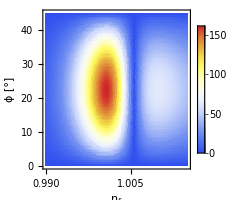

```mathematica
Int=(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dpod})/.minpod[[2]]).WP[#,π].E0))^2))[[1]] &/@ylist;
LeftDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

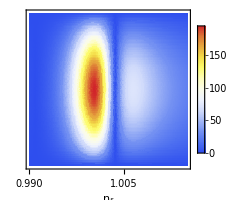

```mathematica
Int=(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[#,π].E0))^2))[[1]] &/@ylist;
RightDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

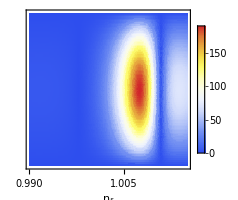

```mathematica
Int=(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.halfopt).WP[#,π].E0))^2))[[1]] &/@ylist;
RightDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

##### Czułość w konkretnym miejscu (ϕ, n_s)

```mathematica
ϕpod=22.5;
ϕopt=20;
podczu=Abs@ND[(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dpod})/.halfopt).WP[(ϕpod π/180.),π].E0))^2))[[1]] ,ns,ns/.nshelu, Terms->30, WorkingPrecision->15]
optczu=Abs@ND[(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[1]]).WP[ϕopt π/180.,π].E0))^2))[[1]] ,ns,ns/.nshelu, Terms->30, WorkingPrecision->15]
optczu/podczu
```

142.176

9.30031

0.0654139

```mathematica
ϕopt1=10;
ϕopt2=18;
opt1czu=Abs@ND[(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[(ϕopt1 π/180.),π].E0))^2))[[1]] ,ns,ns/.nshelu, Terms->20, WorkingPrecision->10]
opt2czu=Abs@ND[(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[ϕopt2 π/180.,π].E0))^2))[[1]] ,ns,ns/.nshelu, Terms->20, WorkingPrecision->10]
opt2czu/opt1czu
```

124.133

183.665

1.47958

```mathematica
ϕopt1=7;
ϕopt2=21;
opt1czu=Abs@ND[(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[(ϕopt1 π/180.),π].E0))^2))[[1]] ,ns,ns/.nshelu, Terms->20, WorkingPrecision->10]
opt2czu=Abs@ND[(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[ϕopt2 π/180.,π].E0))^2))[[1]] ,ns,ns/.nshelu, Terms->20, WorkingPrecision->10]
opt2czu/opt1czu
```

90.663

192.059

2.11839

#### Znormalizowana różnica intensywności polaryzacji s i p

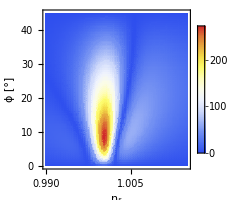

```mathematica
Int=(((Abs@(WP[0.25π,0.5π].((SPR/.{d->dpod})/.minpod[[2]]).WP[#,π].E0))^2)[[1]]/Total@((Abs@(((SPR/.{d->dpod})/.minpod[[2]]).WP[# ,π].E0))^2)) &/@ylist;
LeftDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

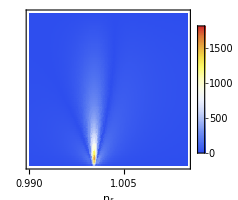

```mathematica
Int=(((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[#,π].E0))^2)[[1]]/Total@((Abs@(((SPR/.{d->dopt})/.minopt[[2]]).WP[# ,π].E0))^2)) &/@ylist;
RightDensityPlot[( Abs@ND[Int,ns,#, Terms->20, WorkingPrecision->10] &/@xlist)ᵀ]
```

#### Przyczyny wzrostu czułości po normalizacji

Artefakt w działaniu DensityPlot’a zmusił mnie do dodania dwóch zer na końcu

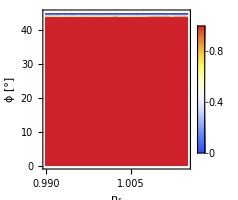

```mathematica
Int=(Total@((Abs@(WP[0.25π,0.5π].WP[#,π].E0))^2)) &/@ylist;
AppendTo[Int,0];
AppendTo[Int,0];
LeftDensityPlot[( (Int/.{ns->#})&/@xlist)ᵀ]
```

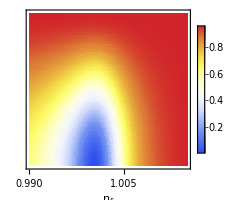

```mathematica
Int=(Total@(((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[#,π].E0))^2))) &/@ylist;
RightDensityPlot[( (Int/.{ns->#})&/@xlist)ᵀ]
```

### Odpowiedź układu

```mathematica
nsmin=0.990;
nsmax=1.015;
phimin=0;
phimax=π/4;
xlist=Table[i,{i,nsmin,nsmax,0.0001}];
ylist=Table[i,{i,phimin,phimax,0.01}];
E0={1,0};
SPR={{rptot[θo[θ Degree],d,λnow],0},{0,rstot[θo[θ Degree],d,λnow]}};
```

#### Różnica intensywności polaryzacji s i p

```mathematica
Int=(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dpod})/.minpod[[2]]).WP[#,π].E0))^2))[[1]] &/@ylist;
LeftDensityPlot[( (Int/.{ns->#})&/@xlist)ᵀ]
```

-Graphics-

```mathematica
Int=(Differences@((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[#,π].E0))^2))[[1]] &/@ylist;
RightDensityPlot[( (Int/.{ns->#})&/@xlist)ᵀ]
```

-Graphics-

#### Znormalizowana różnica intensywności polaryzacji s i p

```mathematica
Int=(((Abs@(WP[0.25π,0.5π].((SPR/.{d->dpod})/.minpod[[2]]).WP[#,π].E0))^2)[[1]]/Total@((Abs@(((SPR/.{d->dpod})/.minpod[[2]]).WP[# ,π].E0))^2)) &/@ylist;
LeftDensityPlot[( (Int/.{ns->#})&/@xlist)ᵀ]
```

-Graphics-

```mathematica
Int=(((Abs@(WP[0.25π,0.5π].((SPR/.{d->dopt})/.minopt[[2]]).WP[#,π].E0))^2)[[1]]/Total@((Abs@(((SPR/.{d->dopt})/.minopt[[2]]).WP[# ,π].E0))^2)) &/@ylist;
RightDensityPlot[( (Int/.{ns->#})&/@xlist)ᵀ]
```

-Graphics-

## Pomiary

### Odpowiedź uproszczonego układu na sygnał trójkątny

```mathematica
file=Import["uporszczony_uklad.CSV","Data"][[2;;All]];
file={100#[[1]],#[[2]],#[[3]],#[[4]]}&/@((fileᵀ-{file[[1,1]],0,0,0})ᵀ);
data={file[[1;;All,{1,2}]],file[[1;;All,{1,3}]],file[[1;;All,{1,4}]]};
ListLinePlot[data,PlotStyle->{Orange,Blue,Purple},Frame->True,FrameLabel->{"t [ms]","U [V]"},AspectRatio->0.7, ImageSize->{plotSize[[1]],200},PlotLegends->{"I_s-I_p","I_s+I_p","U_mod [0.01]"}, GridLines->Automatic]
```

-Graphics-

### Azot

#### Bez dzielnika

##### ϕ=0.5°

```mathematica
AzotPlot["04","05"]
```

-Graphics-

##### ϕ=10.5°

```mathematica
AzotPlot["02","03"]
```

-Graphics-

##### ϕ=22.5°

```mathematica
AzotPlot["01","00"]
```

-Graphics-

#### Z dzielnikiem

##### ϕ=0.5°

```mathematica
AzotPlot["12","13"]
```

-Graphics-

```mathematica
ListPlot@Import["Azot/TEK00012.CSV","Data"]
StandardDeviation@(Import["Azot/TEK00012.CSV","Data"])
```

-Graphics-

{0.00577379,0.0000651866}

##### ϕ=10.5°

```mathematica
AzotPlot["10","11"]
```

-Graphics-

##### ϕ=22.5°

```mathematica
AzotPlot["14","15"]
```

-Graphics-

### Hel

#### Układ podstawowy

##### ϕ=0.5°

```mathematica
HelPlot["TEK00007.CSV",100]
HelPlot["TEK00008.CSV",100]
```

-Graphics-

-Graphics-

(2→0 Atm)

```mathematica
HelPlot["TEK00009.CSV",440]
```

-Graphics-

##### ϕ=22.5°

```mathematica
HelPlot["TEK00001tk.CSV",1,8000]
```

-Graphics-

```mathematica
HelPlot["TEK00010.CSV",2040]
HelPlot["TEK00011.CSV",100]
```

-Graphics-

-Graphics-

#### Układ optymalny

##### ϕ=0.5°

```mathematica
HelPlot["TEK00012.CSV",5500]
```

-Graphics-

##### ϕ=8°

```mathematica
HelPlot["TEK00013.CSV",100]
HelPlot["TEK00014.CSV",100]
```

-Graphics-

-Graphics-

##### ϕ=20°

```mathematica
HelPlot["TEK00015.CSV",200]
HelPlot["TEK00016.CSV",1500]
```

-Graphics-

-Graphics-

```mathematica
StandardDeviation@(Import["Hel/TEK00015.CSV","Data"][[200;;1000]]ᵀ[[2]])
```

0.005786

##### ϕ=30°

```mathematica
HelPlot["TEK00017.CSV",500]
```

-Graphics-

#### Zestawienia

```mathematica
a=Import["Hel/TEK00011.CSV","Data"][[300;;8350,{1,2}]];
data={1#[[1]],Abs@#[[2]]}&/@((aᵀ-{a[[1,1]],a[[1,2]]})ᵀ);
b=Import["Hel/TEK00015.CSV","Data"][[400;;All,{1,2}]];
data2={#[[1]],Abs@#[[2]]}&/@((bᵀ-{b[[1,1]],b[[1,2]]})ᵀ);
Style[ListLinePlot[{data,data2}, Frame->True,PlotLegends-> {"d=d_pod","d=d_opt"}, FrameLabel->{"t [100 ms]","U [V]"}, GridLines->Automatic],"Figure"]
```

-Graphics-